Kitaev Chain |

Spectral Propertiespaclet:QuantumPlaybook/tutorial/KitaevChain#283481385 | Majorana Representationpaclet:QuantumPlaybook/tutorial/KitaevChain#399500441

The Kitaev chain is a prototype example of the topological superconductor. Here, we demonstrate how to examine its properties using Q3. See Kitaev (2001), Kitaev's original, for technical details of the model.

FockNumberpaclet:Q3/ref/FockNumberQ3 Package Symbol or Qpaclet:Q3/ref/QQ3 Package Symbol | Number operator
FockHoppingpaclet:Q3/ref/FockHoppingQ3 Package Symbol or Hoppaclet:Q3/ref/HopQ3 Package Symbol | Constructs the hopping Hamiltonian terms
FockPairingpaclet:Q3/ref/FockPairingQ3 Package Symbol or Pairpaclet:Q3/ref/PairQ3 Package Symbol | Constructs the pairing Hamiltonian terms
ToMajoranapaclet:Q3/ref/ToMajoranaQ3 Package Symbol | Converts Dirac fermions to Majorana fermions.
ToDiracpaclet:Q3/ref/ToDiracQ3 Package Symbol | Converts Majorana fermions to Dirac fermions. 
GraphFormpaclet:Q3/ref/GraphFormQ3 Package Symbol | Visualizes a non-interacting Hamiltonian or corresponding matrix in a graph.
ChiralGraphFormpaclet:Q3/ref/ChiralGraphFormQ3 Package Symbol | Visualizes the off-diagonal block of a matrix with chiral symmetry.

Some useful functions to study the Kitaev chain.

Load Q3.

```mathematica
<<Q3`
```

Let c denote the (Dirac) Fermionpaclet:Q3/ref/FermionQ3 Package Symbol operator.

```mathematica
Let[Fermion,c]
```

Let t, μ, and Δ denote the hopping amplitude, chemical potential, and pairing potential, respectively.

```mathematica
Let[Real,t,μ,Δ]
```

The number of sites in the one-dimensional lattice.

```mathematica
$L=5;
```

Define some Lists of operators to be used later.

```mathematica
cc=c[Range[1,$L]]
cccc=Join[cc,Dagger@cc]
```

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5)}

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5),c_(,,1)^(,,†),c_(,,2)^(,,†),c_(,,3)^(,,†),c_(,,4)^(,,†),c_(,,5)^(,,†)}

Now, construct the model Hamiltonian.

```mathematica
H0=-μ*Q[cc]
Hhop=-t*PlusDagger @ FockHopping[cc]
Hpair=Δ*PlusDagger @ FockPairing[cc]
HH=H0+Hhop+Hpair
```

-μ (c_(,,1)^(,,†)c_(,,1)+c_(,,2)^(,,†)c_(,,2)+c_(,,3)^(,,†)c_(,,3)+c_(,,4)^(,,†)c_(,,4)+c_(,,5)^(,,†)c_(,,5))

-t (c_(,,1)^(,,†)c_(,,2)+c_(,,2)^(,,†)c_(,,1)+c_(,,2)^(,,†)c_(,,3)+c_(,,3)^(,,†)c_(,,2)+c_(,,3)^(,,†)c_(,,4)+c_(,,4)^(,,†)c_(,,3)+c_(,,4)^(,,†)c_(,,5)+c_(,,5)^(,,†)c_(,,4))

Δ (-c_(,,2)c_(,,1)-c_(,,3)c_(,,2)-c_(,,4)c_(,,3)-c_(,,5)c_(,,4)-c_(,,1)^(,,†)c_(,,2)^(,,†)-c_(,,2)^(,,†)c_(,,3)^(,,†)-c_(,,3)^(,,†)c_(,,4)^(,,†)-c_(,,4)^(,,†)c_(,,5)^(,,†))

-Graphics-

Take a look at the connectivity of the model. Here, the black thin lines indicate single-particle tunneling and the red thick lines represent the p-wave pairing.

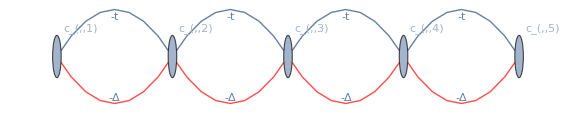

```mathematica
GraphForm[HH]
```

## Spectral Properties

To investigate the quasi-particle spectrum (by means of the Bogoliubov-de Gennes equation), obtain the single-particle BdG Hamiltonian.

```mathematica
matK=CoefficientTensor[HH,Dagger@cccc,cccc];
matK//MatrixForm
```

(-μ/2 | -t/2 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0
-t/2 | -μ/2 | -t/2 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0 | 0
0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | Δ/2 | 0 | -Δ/2 | 0
0 | 0 | -t/2 | -μ/2 | -t/2 | 0 | 0 | Δ/2 | 0 | -Δ/2
0 | 0 | 0 | -t/2 | -μ/2 | 0 | 0 | 0 | Δ/2 | 0
0 | Δ/2 | 0 | 0 | 0 | μ/2 | t/2 | 0 | 0 | 0
-Δ/2 | 0 | Δ/2 | 0 | 0 | t/2 | μ/2 | t/2 | 0 | 0
0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | t/2 | μ/2 | t/2 | 0
0 | 0 | -Δ/2 | 0 | Δ/2 | 0 | 0 | t/2 | μ/2 | t/2
0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | 0 | t/2 | μ/2)

Now, study the quasi-particle energy spectrum of the model. Be aware of the finite size effects.

```mathematica
KK[a_,b_,c_]:=Block[{μ=a,t=b,Δ=c},SparseArray@ArrayRules@matK]
```

```mathematica
Manipulate[
Module[
{eval=Table[Sort@Eigenvalues[KK[μ,1.,del]],{μ,0,4,0.02}]},
ListLinePlot[Transpose@eval,
Axes->None,
Frame->True,
FrameLabel->{"μ / t","Eenergy / t"},
DataRange->{0,4}]
],
{{del,1,"Δ"},0.5,2,0.1},
SaveDefinitions->True]
```

## Majorana Representation

```mathematica
Let[Majorana,a]
```

```mathematica
aa=a@Range[2*$L]
```

{a_(,,1),a_(,,2),a_(,,3),a_(,,4),a_(,,5),a_(,,6),a_(,,7),a_(,,8),a_(,,9),a_(,,10)}

Rewrite the Hamiltonian in terms of the Majorana fermions.

```mathematica
MM=ToMajorana[HH,cc->aa]
```

-(5 μ)/2-1/2 ⅈ μ a_(,,1)a_(,,2)-1/2 ⅈ (t-Δ) a_(,,1)a_(,,4)+1/2 ⅈ (t+Δ) a_(,,2)a_(,,3)-1/2 ⅈ μ a_(,,3)a_(,,4)-1/2 ⅈ (t-Δ) a_(,,3)a_(,,6)+1/2 ⅈ (t+Δ) a_(,,4)a_(,,5)-1/2 ⅈ μ a_(,,5)a_(,,6)-1/2 ⅈ (t-Δ) a_(,,5)a_(,,8)+1/2 ⅈ (t+Δ) a_(,,6)a_(,,7)-1/2 ⅈ μ a_(,,7)a_(,,8)-1/2 ⅈ (t-Δ) a_(,,7)a_(,,10)+1/2 ⅈ (t+Δ) a_(,,8)a_(,,9)-1/2 ⅈ μ a_(,,9)a_(,,10)

Examine the connectivity through the single-particle Hamiltonian.

```mathematica
matM=CoefficientTensor[MM,aa,aa];
matM//MatrixForm
```

(0 | -(ⅈ μ)/4 | 0 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ μ)/4 | 0 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ⅈ t)/4-(ⅈ Δ)/4 | 0 | -(ⅈ μ)/4 | 0 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0
(ⅈ t)/4-(ⅈ Δ)/4 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | 0 | -(ⅈ μ)/4 | 0 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0
0 | 0 | (ⅈ t)/4-(ⅈ Δ)/4 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | 0 | -(ⅈ μ)/4 | 0 | -(ⅈ t)/4+(ⅈ Δ)/4
0 | 0 | 0 | 0 | (ⅈ t)/4-(ⅈ Δ)/4 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/4+(ⅈ Δ)/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | 0 | -(ⅈ μ)/4
0 | 0 | 0 | 0 | 0 | 0 | (ⅈ t)/4-(ⅈ Δ)/4 | 0 | (ⅈ μ)/4 | 0)

Here, factor 4I is just for convenience and simplifies the coefficients.

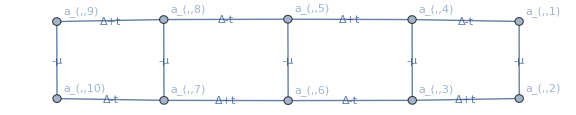

```mathematica
GraphForm[4*I*matM//SimplifyThrough,VertexLabels->aa]
```

The chiral symmetry (i.e., anti-symmetry or sub-lattice symmetry) becomes clearer by first consider the special case t=Δ as below.

### Special Case: t=Δ

Let us consider a special case: t=Δ.

```mathematica
JJ=Block[{Δ=t},MM]
```

-(5 μ)/2-1/2 ⅈ μ a_(,,1)a_(,,2)+ⅈ t a_(,,2)a_(,,3)-1/2 ⅈ μ a_(,,3)a_(,,4)+ⅈ t a_(,,4)a_(,,5)-1/2 ⅈ μ a_(,,5)a_(,,6)+ⅈ t a_(,,6)a_(,,7)-1/2 ⅈ μ a_(,,7)a_(,,8)+ⅈ t a_(,,8)a_(,,9)-1/2 ⅈ μ a_(,,9)a_(,,10)

Examine the connectivity.

```mathematica
matJ=CoefficientTensor[JJ,aa,aa];
matJ//MatrixForm
```

(0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | (ⅈ t)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | 0 | -(ⅈ μ)/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0)

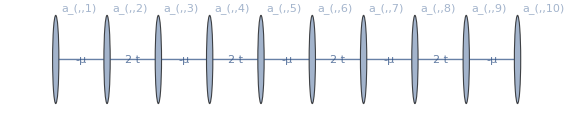

```mathematica
GraphForm[4*I*matJ//SimplifyThrough,VertexLabels->aa]
```

The above graph clearly shows the chiral (i.e. sublattice) symmetry. To make it clearer, rearrange the Majorana modes.

```mathematica
ab=Transpose@Partition[aa,2]
```

{{a_(,,1),a_(,,3),a_(,,5),a_(,,7),a_(,,9)},{a_(,,2),a_(,,4),a_(,,6),a_(,,8),a_(,,10)}}

```mathematica
matC=CoefficientTensor[JJ,Flatten@ab,Flatten@ab];
matC//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -(ⅈ μ)/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | -(ⅈ μ)/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | -(ⅈ μ)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | -(ⅈ μ)/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/2 | -(ⅈ μ)/4
(ⅈ μ)/4 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ⅈ μ)/4 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (ⅈ μ)/4 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ⅈ μ)/4 | (ⅈ t)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0)

The  block-off diagonal structure of the above matrix demonstrates the chiral symmetry.

```mathematica
matD=CoefficientTensor[JJ,First@ab,Last@ab];
matD//MatrixForm
```

(-(ⅈ μ)/2 | 0 | 0 | 0 | 0
-ⅈ t | -(ⅈ μ)/2 | 0 | 0 | 0
0 | -ⅈ t | -(ⅈ μ)/2 | 0 | 0
0 | 0 | -ⅈ t | -(ⅈ μ)/2 | 0
0 | 0 | 0 | -ⅈ t | -(ⅈ μ)/2)

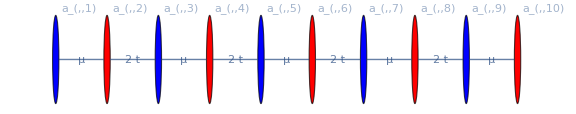

```mathematica
ChiralGraphForm[2*I*matD,VertexLabels->ab]
```

### Back to General Case

Motivated by the above special case, we now examine again the general case with the rearranged Majorana modes.

```mathematica
matM=CoefficientTensor[MM,Flatten@ab,Flatten@ab];
matM//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -(ⅈ μ)/4 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | -(ⅈ μ)/4 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | -(ⅈ μ)/4 | -(ⅈ t)/4+(ⅈ Δ)/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | -(ⅈ μ)/4 | -(ⅈ t)/4+(ⅈ Δ)/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ t)/4-(ⅈ Δ)/4 | -(ⅈ μ)/4
(ⅈ μ)/4 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ t)/4-(ⅈ Δ)/4 | (ⅈ μ)/4 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (ⅈ t)/4-(ⅈ Δ)/4 | (ⅈ μ)/4 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (ⅈ t)/4-(ⅈ Δ)/4 | (ⅈ μ)/4 | (ⅈ t)/4+(ⅈ Δ)/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (ⅈ t)/4-(ⅈ Δ)/4 | (ⅈ μ)/4 | 0 | 0 | 0 | 0 | 0)

```mathematica
matN=CoefficientTensor[MM,First@ab,Last@ab];
matN//MatrixForm
```

(-(ⅈ μ)/2 | -1/2 ⅈ (t-Δ) | 0 | 0 | 0
-1/2 ⅈ (t+Δ) | -(ⅈ μ)/2 | -1/2 ⅈ (t-Δ) | 0 | 0
0 | -1/2 ⅈ (t+Δ) | -(ⅈ μ)/2 | -1/2 ⅈ (t-Δ) | 0
0 | 0 | -1/2 ⅈ (t+Δ) | -(ⅈ μ)/2 | -1/2 ⅈ (t-Δ)
0 | 0 | 0 | -1/2 ⅈ (t+Δ) | -(ⅈ μ)/2)

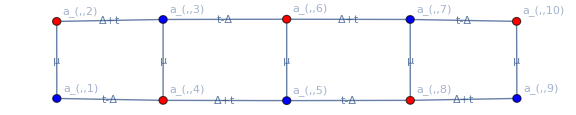

```mathematica
ChiralGraphForm[2*I*matN,VertexLabels->ab]
```

| Related Guides
▪Quantum Many-Body Systems

| Related Tech Notes
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪A. Kitaev, Physics-Uspekhi 44, 131 (2001)https://doi.org/10.1070/1063-7869/44/10S/S29, "Unpaired Majorana fermions in quantum wires".
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).